# Complex Variables Mathematical Toolbox

## Nathan Yee

## Importing the library

To use the library in any of my Mathematica notebooks I simply need to write the following lines

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<complexToolkit.m
```

Next let's test the the library - use ?

```mathematica
?fSpace
```

fSpace[min, max, steps, Log] gives (default) log spaced points from min to max over a given number of points

or press ctr + shift + K to auto complete

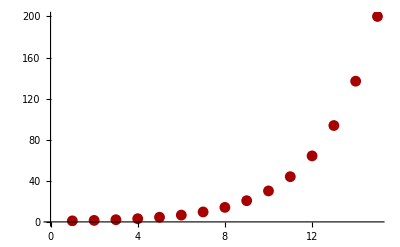

```mathematica
ListPlot[fSpace[1, 200, 15, Log]]
```

## Newton’s Method

```mathematica
Unprotect[f]
```

{}

```mathematica
f[z_]:=z^3-1
```

```mathematica
map=(z-f[z]/f'[z])
```

z-(-1+z^3)/(3 z^2)

```mathematica
gridPts=makeGrid[-3,3,200,3];
```

```mathematica
?makeExponentialSpacedCirclePoints
```

Notebook$$18$484803`makeExponentialSpacedCirclePoints

makeExponentialSpacedCirclePoints[smallRadius_,largeRadius_,numCircles_,ptsPerCircle_]:=Module[{ang,lists,pts},ang=Range[0 π,2 π,(2 π+0)/(ptsPerCircle-1)];lists=Table[{r Cos[ang],r Sin[ang]},{r,fSpace[smallRadius,largeRadius,numCircles]}];pts=(Transpose[#1]&)/@lists;Return[pts]]

```mathematica
gridPts = makeExponentialSpacedCirclePoints[.1,5,10,100];
```

```mathematica
With[{range=5},
plots=Flatten[{
{ListPlot[gridPts,PlotRange->{{-range,range}, {-range,range}},PlotStyle->PointSize[.02],AspectRatio->1]},
Table[
(*Apply map to grid pts*) gridPts=getImagePts[map,gridPts];
ListPlot[gridPts,PlotRange->{{-range,range}, {-range,range}},PlotStyle->PointSize[.02],AspectRatio->1]
,{n,1,36}]
}];
]
```

```mathematica
Manipulate[plots[[n]],{n,1,Length[plots],1}]
```

## 3D printing

### Second level section heading

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

#### Third level section heading

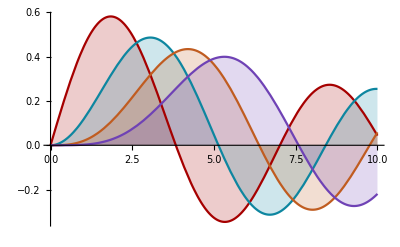

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.